```mathematica
root = "/pool/isilon/genomics/frandsenp/bees";
datadir = FileNameJoin[{root, "images4nets"}];
bifariousdir=FileNameJoin[{datadir, "B_bifarious_cropped"}];
melanopygusdir = FileNameJoin[{datadir, "B_melanopygus_cropped"}];
bifarfiles=FileNames["*.jpg", bifariousdir];
melanofiles = FileNames["*.jpg", melanopygusdir];
{Length@bifarfiles, Length@melanofiles}
```

{6212,5692}

```mathematica
Needs["CUDALink`"]
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx10g"];
```

```mathematica
bifardat=ParallelMap[Import[#]&,bifarfiles];
melanodat=ParallelMap[Import[#]&,melanofiles];
```

```mathematica
{Dimensions@bifardat, Dimensions@melanodat}
```

{{6212},{5692}}

```mathematica
RandomSample[bifardat, 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[melanodat,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dat=RandomSample@Join[Thread[bifardat->"bifar"],Thread[melanodat->"melano"]];
Dimensions@dat
```

{11904}

```mathematica
RandomSample[dat,30]
```

{-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→bifar,-Graphics-→melano}

```mathematica
bifEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,bifardat];
melEntropy=ParallelMap[ImageMeasurements[#,"Entropy"]&,melanodat];
```

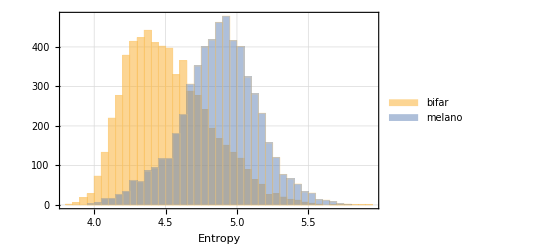

```mathematica
Histogram[{bifEntropy,melEntropy},40,ChartLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

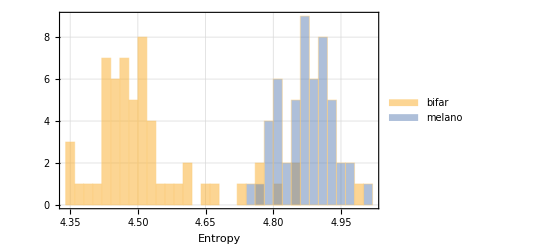

```mathematica
Histogram[{Map[Mean,Partition[bifEntropy,108]],Map[Mean,Partition[melEntropy,108]]},40,ChartLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

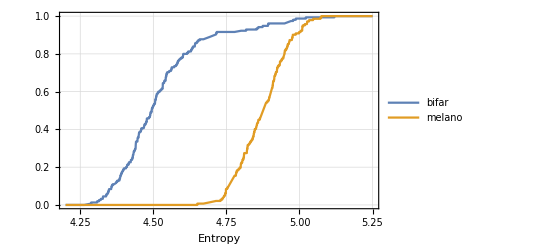

```mathematica
Plot[{CDF[EmpiricalDistribution[Map[Mean, Partition[bifEntropy,40]]],x], CDF[EmpiricalDistribution[Map[Mean, Partition[melEntropy, 40]]],x]},{x,4.2,5.25},PlotLegends->{"bifar","melano"},GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],Frame->True,FrameLabel->{Style["Entropy",FontSize->14]}]
```

```mathematica
rs=RandomSample[Range[Length[dat]]];
tix=rs[[1;;Round[Length[dat]*0.7]]];
vix=rs[[Round[Length[dat]*0.7]+1;;Round[Length[dat]*0.9]]];
ttix=rs[[Round[Length[dat]*0.9]+1;;]];
{Length@tix,Length@vix,Length@ttix}
```

{8333,2381,1190}

```mathematica
networkdir=FileNameJoin[{root,"networks"}];
net=NetChain[
{
ConvolutionLayer[10,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},{2,2}],
ConvolutionLayer[20,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[40,{5,5}],
BatchNormalizationLayer[],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DropoutLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"bifar","melano"}}],
"Input"->NetEncoder[{"Image",{220,298}}]
]
```

NetChain[]

```mathematica
net=NetTrain[net,dat[[tix]],ValidationSet->dat[[vix]],TargetDevice->"GPU","Method"->{"ADAM","L2Regularization"->5,"InitialLearningRate"->0.0001}];
```

```mathematica
cm=ClassifierMeasurements[net,dat[[ttix]]];
```

```mathematica
cm["Accuracy"]
```

0.971429

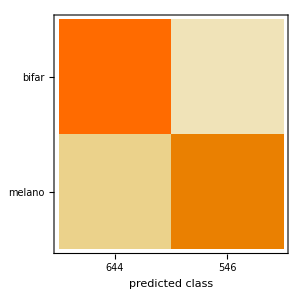

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
testDatBifar=Select[dat[[ttix]],Values@#=="bifar"&];
testDatMelano=Select[dat[[ttix]],Values@#=="melano"&];
```

```mathematica
pTestDatBifar=net[Keys@testDatBifar,{"Probability","bifar"}];
pTestDatMelano=net[Keys@testDatMelano,{"Probability","bifar"}];
```

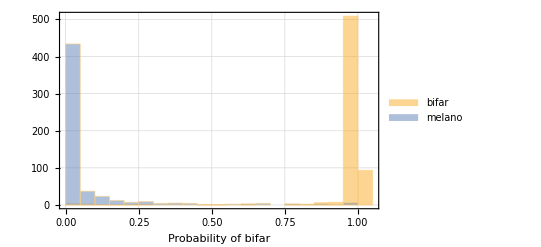

```mathematica
Histogram[{pTestDatBifar,pTestDatMelano},20,GridLines->Automatic,GridLinesStyle->Directive[Dotted,Gray],Frame->True,FrameLabel->{"Probability of bifar"},ChartLegends->{"bifar","melano"}]
```

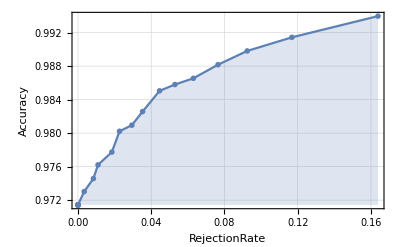

```mathematica
Show[
cm["AccuracyRejectionPlot"],
GridLines->Automatic,
GridLinesStyle->Directive[Dotted, Gray]
]
```